```mathematica
a = Import["day24input.txt"] // StringReplace[{StartOfLine~~"0/" -> "0->", "/" -> "<->"}] // ImportString[#, "List"]& // ToExpression;
```

```mathematica
g = Graph[a];
```

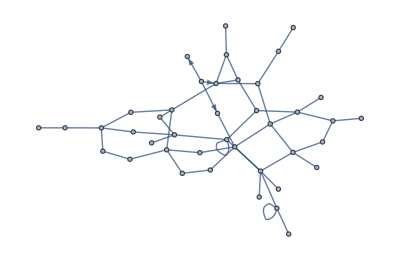

```mathematica
subgraph = NeighborhoodGraph[g, 0, Length@EdgeList@g]
```

```mathematica
edges = EdgeList@subgraph
```

{24<->14,30<->24,29<->29,29<->44,44<->30,47<->37,6<->14,20<->37,20<->24,0->45,14<->45,47<->45,5<->5,44<->5,5<->37,26<->44,2<->31,5<->31,19<->40,40<->44,40<->24,47<->11,45<->11,36<->31,3<->32,30<->35,32<->41,41<->35,0->39,39<->30,46<->50,41<->50,50<->36,45<->50,49<->41,49<->4,4<->30,38<->20,38<->23,23<->40,0->43,20<->16,34<->38,22<->17,17<->3,2<->17,46<->17,9<->11,22<->48,6<->28,29<->12,21<->31,18<->44}

```mathematica
starts = EdgeList[subgraph, 0 <-> _]
```

{0->45,0->39,0->43}

```mathematica
sum[path_]:=Total@(Total /@ path)
```

```mathematica
maxSum=0; maxLength=0;
```

```mathematica
findPath[edge_, vertex_, path_] := Module[{other, nextEdges, tmpSum},
other = If[First@edge == vertex,Last@edge,First@edge];
nextEdges = Complement[EdgeList[subgraph, other <->_], path];
If[Length@nextEdges == 0,
tmpSum = sum[path];
If[tmpSum > maxSum,
maxSum = tmpSum;
maxSumPath = path;
];
If[Length@path > maxLength,
maxLength = Length@path;
maxLengthPath = path,
If[Length@path == maxLength && sum@path > sum@maxLengthPath,
maxLengthPath = path;
]
],
Scan[findPath[#, other, Union[path, {#}]]&,nextEdges];
]
]
```

```mathematica
Scan[findPath[#, 0, {#}]&,starts]
```

```mathematica
part1 =maxSum
```

2006

```mathematica
part2 = sum@maxLengthPath
```

1994

```mathematica
HighlightGraph[subgraph, maxSumPath]
```

-Graphics-

```mathematica
HighlightGraph[subgraph, maxLengthPath]
```

-Graphics-